```mathematica
(*(e,n)=(185,76073)
メッセージ:{49035,55808,48104,71314,13972,18838,75671,40307,55111,75671,71314,71314,55808,13972,28380,22910,70445,75671,48104,75671,38382,68165}
*)
Divisors[76073]
```

{1,127,599,76073}

```mathematica
ExtendedGCD[185,(127-1)*(599-1)]
```

{1,{-2851,7}}

```mathematica
-2851+(127-1)*(599-1)
```

72497

```mathematica
Mod[Function[x,x^72497]/@{49035,55808,48104,71314,13972,18838,75671,40307,55111,75671,71314,71314,55808,13972,28380,22910,70445,75671,48104,75671,38382,68165},76073]
```

{84,101,115,116,32,71,97,110,98,97,116,116,101,32,75,117,100,97,115,97,105,46}

```mathematica
FromCharacterCode[%]
```

```mathematica
"Test Ganbatte Kudasai."
```

```mathematica
(*Q3*)
compNumber[n_]:=
If[n<1,1,RandomPrime[{2^n  ,2^(n+1)-1}]RandomPrime[{2^n,2^(n+1)}]]
```

```mathematica
decompTime[n_]:=Part[Timing[FactorInteger[compNumber[n]]],1]
```

```mathematica
decompTime[85]
```

10.5523

```mathematica
(*だいたい１０秒くらいで終わるのは85であった*)
```

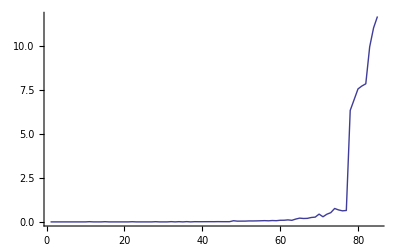

```mathematica
ListPlot[Table[decompTime[i],{i,1,85}],Joined->True,PlotRange->All]
```